## Newton — Problem Set 3 Solution

### 1. Problem 1

(a) By the definition of the radian, this is simply, rθ, and since r=1,  len(arc AB)=θ. The length of AD is given by the tangent:  len(AD)=tanθ.

(b) The chord we are looking for is twice half the chord. But half the chord (by the hint) is sin θ/2. So the full chord is 2sin θ/2.

(c) For 1 radian: θ=1, tanθ=1.55740772465, and 2sin θ/2=0.9588510772.
For 0.1 radian: θ=0.1, tanθ=0.10033467208, and 2sin θ/2=0.09995833854. Oh my, this is looking promising.
For 0.01 radian: θ=0.01, tanθ=0.01000033334, and 2sin θ/2=0.00999995833. 

Let us do some ratios. For 1 radian: tanθ/θ=1.557407724, and (2sin θ/2)/θ=0.95885107.
For 0.1 radian: tanθ/θ=1.003346720, and (2sin θ/2)/θ=0.999583385.
For 0.01 radian: tanθ/θ=1.000033334, and (2sin θ/2)/θ=0.999995833.

So the ratios are improving (tending toward unity). In the first case, only the leading digit agrees with unity. In the second case, 3 or 4 digits agree with unity. In the third case, 5 or 6 digits agree with unity.

### 2. Arc Lengths and Chord Lengths of Parabolas

(a) The chord length from (0, 0) to the point (a, a^2) is√(a^2+ a^4) by the Pythagorean theorem.

(b) The chord lengths and arc lengths for a = 3, a = 1, and a = 1/3 are below. I added a=1/10 in my answer.

```mathematica
pThree=N[{Sqrt[a^2+a^4],1/2 a Sqrt[1+4 a^2]+1/4 Log[2a+Sqrt[1+4 a^2]]}/.a->3]
```

{9.48683,9.74709}

```mathematica
pOne=N[{Sqrt[a^2+a^4],1/2 a Sqrt[1+4 a^2]+1/4 Log[2a+Sqrt[1+4 a^2]]}/.a->1]
```

{1.41421,1.47894}

```mathematica
pOneThird=N[{Sqrt[a^2+a^4],1/2 a Sqrt[1+4 a^2]+1/4 Log[2a+Sqrt[1+4 a^2]]}/.a->1/3]
```

{0.351364,0.356595}

```mathematica
pOneTenth=N[{Sqrt[a^2+a^4],1/2 a Sqrt[1+4 a^2]+1/4 Log[2a+Sqrt[1+4 a^2]]}/.a->1/10]
```

{0.100499,0.100663}

```mathematica
pThree[[1]]/pThree[[2]]
```

0.973299

```mathematica
pOne[[1]]/pOne[[2]]
```

0.956233

```mathematica
pOneThird[[1]]/pOneThird[[2]]
```

0.985332

```mathematica
pOneTenth[[1]]/pOneTenth[[2]]
```

0.998371

The ratios are generally getting better, but the case a=1 was an outlier.

### 3. Lemma 8 applied to Circles

(a) The area of the three-sided figure which has two of the sides as radii and one side as the arc is θ/(2π) of the area of the whole circle, so it is θ/(2π)π=θ/2. For the triangle, it is 1/2 bh=1/2 tanθ.

(b) Using the same bisecting trick, we have two triangles, each of which has area 1/2 bh. So together they are bh. Their heights are sin θ/2. Their bases are cos θ/2. So the final result using the double-angle identity for the sine function is sinθ/2.

(c) For 1 radian: θ/2=0.5, tanθ/2=0.77870386232, and sinθ/2=0.4207354924.
For 0.1 radian: θ/2=0.05, tanθ/2=0.05016733604, and sinθ/2=0.04991670832.
For 0.01 radian: θ/2=0.005, tanθ/2=0.00500016667, and sinθ/2=0.00499991666.

Let us do some ratios. For 1 radian: tanθ/θ=1.557407724, and sinθ/θ=0.8414709848.
For 0.1 radian: tanθ/θ=1.00334672085, and sinθ/θ=0.99833416646.
For 0.01 radian: tanθ/θ=1.00003333467, and sinθ/θ=0.99998333341.

So the ratios of areas are improving (tending toward unity), the same way as they did for the ratios of lengths.

### 4. Lemma 10 — An Example

(a) Plot x(t)=1 meter(1-cos(t radian)/(1 second)):

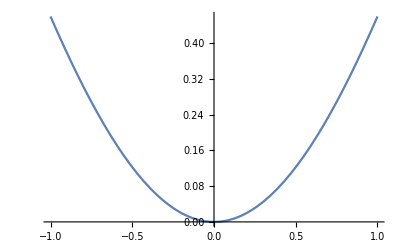

```mathematica
Plot[1-Cos[t], {t, -1, 1}]
```

(b) Superimpose onto this graph a graph of the function x(t) = 1/2(1 meter) (t/(1 second))^2:

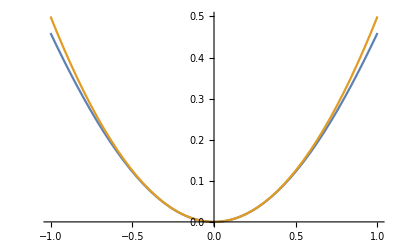

```mathematica
Plot[{1-Cos[t],1/2 t^2}, {t, -1, 1}]
```

(c) Evaluate and compare x(t)=1 meter(1-cos(t radian)/(1 second)) and x(t)= 1/2(1 meter) (t/(1 second))^2 for t = 1 second, t = 0.5 seconds, t=0.25 seconds and t = 0.125 seconds.

```mathematica
x1[t_]:=1-Cos[t]
```

```mathematica
x2[t_]:=1/2 t^2
```

```mathematica
MatrixForm[N[Table[{t, x1[t], x2[t],x1[t]/x2[t]},{t,{ 1, 0.5, 0.25, 0.125}}]]]
```

(1. | 0.459698 | 0.5 | 0.919395
0.5 | 0.122417 | 0.125 | 0.97934
0.25 | 0.0310876 | 0.03125 | 0.994803
0.125 | 0.00780233 | 0.0078125 | 0.998699)

(c) The last column in the table shows how the ratios are improving (tending toward unity).